```mathematica
M[f_,x_]:=Module[{df,ddf,s,sl,i,x0,y,y2},df=D[f,x]//Simplify;
Print["f'=",df];s=x/.Solve[df==0,x,Reals];
If[s==x,Print["极值不存在或函数是奇异的"];Return[]];
s=Union[s]//FullSimplify;
sl=Length[s];If[sl==0,Print["极值不存在或函数是奇异的"];Return[]];
ddf=D[df,x]//Simplify;Print["f''=",ddf];For[i=1,i≤sl,i++,x0=s[[i]];
y=f/.x-> x0;y2=ddf/.x -> x0;p1=y2>0;p2=y2<0;
If[Head[y]==ConditionalExpression,y=Apply[FullSimplify,y]];
If[Head[p1]==ConditionalExpression,p1=Apply[FullSimplify,p1];p2=Apply[FullSimplify,p2]];
If[p1,Print["在 ",x,"=",x0," 处有极小值 ",y],If[p2,Print["在 ",x,"=",x0," 处有极大值 ",y],Print["在 ",x,"=",x0," 处判定失败 "]],Print["在 ",x,"=",x0," 处判定失败 "]]]]
```

```mathematica
M[(x-1)^2 x^3,x]
```

f'=x^2 (3-8 x+5 x^2)

f''=2 x (3-12 x+10 x^2)

在 x=0 处判定失败

在 x=3/5 处有极大值 108/3125

在 x=1 处有极小值 0

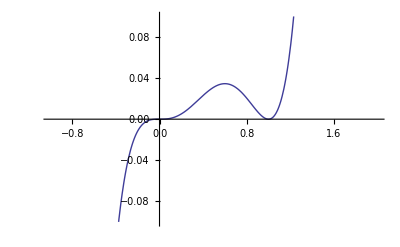

```mathematica
Plot[(x-1)^2 x^3,{x,-1,2},PlotRange->{-0.1,0.1}]
```

```mathematica
M[(3s^2+4s+4)/(s^2+s+1),s]
```

f'=-(s (2+s))/((1+s+s^2)^2)

f''=(2 (-1+3 s^2+s^3))/((1+s+s^2)^3)

在 s=-2 处有极小值 8/3

在 s=0 处有极大值 4

```mathematica
M[1-(2-x)^(2/3),x]
```

f'=2/(3 (2-x)^(1/3))

极值不存在或函数是奇异的

```mathematica
M[Exp[x]Cos[x],x]
```

f'=ⅇ^x (Cos[x]-Sin[x])

f''=-2 ⅇ^x Sin[x]

在 x=ConditionalExpression[1/4 π (1+8 C[1]),C[1]∈Integers] 处有极大值 ⅇ^(1/4 π (1+8 C[1]))/(√2)

在 x=ConditionalExpression[1/4 π (-3+8 C[1]),C[1]∈Integers] 处有极小值 -ⅇ^(1/4 π (-3+8 C[1]))/(√2)